```mathematica
(*Reproducing figures*)
DSolve[{x'[t]==(x[t])*(1-x[t]),x[0]==x0},x[t],t]
```

DSolve::dsfun: (ⅇ^t x0)/(1+ⅇ^t x0) cannot be used as a function.

DSolve[{-(ⅇ^(2 t) x0^2)/((1+ⅇ^t x0)^2)+(ⅇ^t x0)/(1+ⅇ^t x0)==(ⅇ^t x0 (1-(ⅇ^t x0)/(1+ⅇ^t x0)))/(1+ⅇ^t x0),x0/(1+x0)==x0},(ⅇ^t x0)/(1+ⅇ^t x0),t]

```mathematica
x[t_]:=(E^t*x0)/(1-x_0+E^t*x0)
```

```mathematica
xp[t_] := x[t]*(1-x[t])
```

```mathematica
x[2]
```

(ⅇ^2 x0)/(1+ⅇ^2 x0)

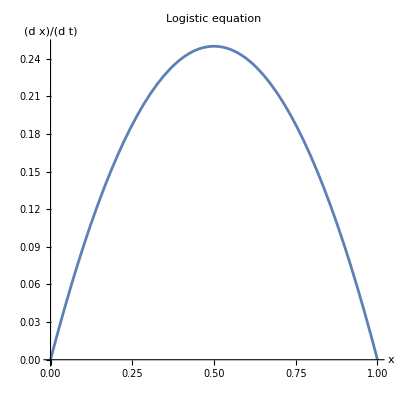

```mathematica
Plot[u*(1-u),{u, 0,1}, AspectRatio->1,AxesLabel->{HoldForm[x],HoldForm[]},PlotLabel->HoldForm[Logistic equation],LabelStyle->{GrayLevel[0]}]
```

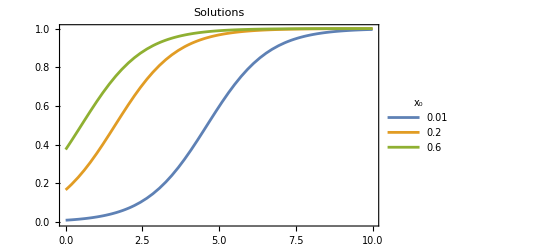

```mathematica
Plot[Evaluate[Table[x[t],{x0,{0.01,0.2,0.6}}]],{t,0,10}, Frame->True,
PlotLegends->LineLegend[Table[x0,{x0,{0.01,0.2,0.6}}],LegendLabel->Subscript[x, 0]],
PlotLabel->HoldForm[Solutions],LabelStyle->{GrayLevel[0]}]
```

```mathematica
(*Finding Equilibrium points*)
Solve[{}]
```